```mathematica
(* Initialisation *)
(* Evaluate before starting writing "real code" *)
(* Usage e.g.: "ld [Spacekey]" becomes "⊨", so writing "a ld 5" turns into "a⊨5" *) 
SetOptions[EvaluationNotebook[], 
			 InputAutoReplacements -> { (* special AceGen assignment operators: *) "ld"-> "⊨","ls"->"⊢","rd"->"⫤","rs"->"⊣",
					                                 (* brackets and symbols: *) "dbl"->"⟦","dbr"->"⟧","lcb"->"{","rcb"->"}","lsb"->"[","rsb"->"]","->"->"→",
					                                 (* shortcuts for starting/ending a comment block: *) "co"->"(*","cc"->"*)"
					                              }
		   ]
(* Output the current time, so we know when AceGen has been executed the last time *)
Now
```

Fri 14 Jun 2024 13:07:27GMT+2

```mathematica
(* Clear all old variables initially to have a fresh start *)
ClearAll["Global`*"] 
(* Start AceGen *) 
<<AceGen`;

NAME = "SMSDo_SMSD";
SMSInitialize[NAME,"Language"-> "Matlab","Mode"-> "Optimal"]; 

(* Define the maximum number of Newton-Raphson iterations, as this also defines the size of convergenceHistory$$ *) 
n iterations = 20;

(* Start a module, which represents the to be created function, with name "NAME" and the specified input and output arguments *) 
SMSModule[NAME,Real[ displacement$$, parameter$$, convergedValue$$, convergenceHistory$$[2,n iterations] ],
		"Input"-> { displacement$$, parameter$$ },
		"Output" -> { convergedValue$$, convergenceHistory$$ }
	       ];
displacement ⊨ SMSReal[ displacement$$ ];
parameter ⊨ SMSReal[ parameter$$ ];
```

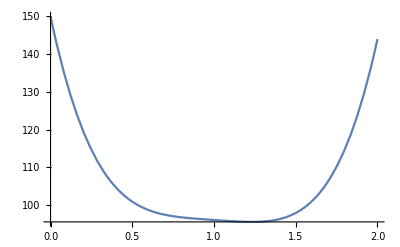

```mathematica
(* Define some energy function and plot it with an exemplary parameter=1 *) 
W energy[utmp_,parameter_]:=( 1/2 * 100 * (utmp-parameter)^4+utmp^2 -5utmp+100);
Plot[W energy[x,1],{x,0,2}]
```

```mathematica
(* #1 Works. *) 
SMSDo[i NR,1,n iterations,1,displacement];
	(* Compute the energy to be minimised using the variable displacement *) 
	  W ⊨ W energy[displacement,parameter];
	(* Find the mininum of the energy W by computing the slope of the energy which will be iteratively computed to find the minimum (R=0) *) 
	  R ⊨ SMSD[W,displacement];
	(* Give some output on the progress and export it to convergenceHistory$$ *) 
           SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
           SMSExport[displacement,convergenceHistory$$[i NR,1]];
           SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSPrintMessage["converged"];
		(* Leave the SMSDo-Loop *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSPrintMessage["failed"];
		(* Leave the SMSDo-Loop *) 
		SMSBreak[];
          SMSEndIf[];
	dRdu ⊨ SMSD[R, displacement];
	displacement ⊣ displacement - 1/dRdu * R;
SMSEndDo[displacement];

SMSExport[displacement,convergedValue$$];
SMSPrintMessage["du/dparameter_out=",SMSD[displacement, parameter]];
```

```mathematica
(* #2 Wrong. The loop works, but the internal derivative is wrong.
SMSDo[i NR,1,n iterations,1,displacement];
	W ⊨ W energy[displacement,parameter];
	R ⊨ SMSD[W,displacement];
      (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSPrintMessage["converged"];
		SMSExport[displacement,convergedValue$$];
		SMSPrintMessage["du/dparameter_in =",SMSD[displacement, parameter]]; (* here the derivative is zero, because the downstream dependence of "displacement" on "R" and "R" on "parameter" is not seen *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
	dRdu ⊨ SMSD[R, displacement];
	displacement ⊣ displacement - 1/dRdu * R;
SMSEndDo[];
*)
```

```mathematica
(* #3 Wrong/zero subderivative inside, but correct derivative outside. 
SMSDo[i NR,1,n iterations,1,displacement];
	W ⊨ W energy[displacement,parameter];
	R ⊨ SMSD[W,displacement];
      (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSPrintMessage["converged"];
		SMSPrintMessage["du/dparameter_in =",SMSD[displacement, parameter]]; (* here the derivative is zero, because the downstream dependence of "displacement" on "R" and "R" on "parameter" is not seen *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
	dRdu ⊨ SMSD[R, displacement];
	displacement ⊣ displacement - 1/dRdu * R;
SMSEndDo[displacement];

SMSPrintMessage["du/dparameter_out=",SMSD[displacement, parameter]]; (* the outside derivative is correct *) 
SMSExport[displacement,convergedValue$$];
*)
```

```mathematica
(* #4 Works. Compute the local derivative using AD but with some manual help in two steps 
SMSDo[i NR,1,n iterations,1,displacement];
	W ⊨ W energy[displacement,parameter];
	R ⊨ SMSD[W,displacement];
	dRdu ⊨ SMSD[R, displacement]; (* Now compute dRdu directly here as it is needed in case of convergence *) 
      (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ];
		SMSPrintMessage["converged"];
		SMSPrintMessage["dR/dparameter_in =",SMSD[R, parameter, "Constant"->displacement]]; (* Computing dR/dparameter is possible as "R=R(parameter)" is known upstream. *) 
		SMSPrintMessage["du/dparameter_in =",-1/dRdu * SMSD[R, parameter, "Constant"->displacement]]; (* Computing du/dparameter based on known update relation *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
	displacement ⊣ displacement - 1/dRdu * R;
SMSEndDo[displacement];

SMSPrintMessage["du/dparameter_out=",SMSD[displacement, parameter]];
SMSExport[displacement,convergedValue$$];
*)
```

```mathematica
(* #5 Works. Change the order of the expressions. Note, several side effects!
SMSDo[i NR,1,n iterations,1,displacement];
	W ⊨ W energy[displacement,parameter];
	R ⊨ SMSD[W,displacement];
      (* Give some output on the progress and export it to convergenceHistory$$ *) 
         SMSPrintMessage["iteration i_NR=",i NR,": W=",W,"; R=",R, "; SMSAbs[R]=",SMSAbs[R]];
         SMSExport[displacement,convergenceHistory$$[i NR,1]];
         SMSExport[SMSAbs[R],convergenceHistory$$[i NR,2]];
	dRdu ⊨ SMSD[R, displacement];
         (* Now "displacement" is updated before checking for convergence *) 
	displacement ⊣ displacement - 1/dRdu * R;
         (* Check the residual for convergence *) 
	SMSIf[ SMSAbs[R]<1*^-8 ]; (* Note that now the convergence check is done for R_k, which was computed from the old displacement (_k), not the updated one (_k+1) in the previous equation *) 
		SMSPrintMessage["converged"];
		SMSPrintMessage["du/dparameter_in =",SMSD[displacement, parameter]]; (* here the correct derivative is computed *) 
		SMSBreak[];
	SMSEndIf[];
          (* If the maximum number of Newton-Raphson iterations is reached, we output the current value and report a convergence failure *) 
          SMSIf[ i NR >=n iterations];
		SMSPrintMessage["failed"];
		SMSBreak[];
          SMSEndIf[];
SMSEndDo[displacement];

SMSPrintMessage["du/dparameter_out=",SMSD[displacement, parameter]];
SMSExport[displacement,convergedValue$$]; *)
```

```mathematica
(* @todo Add more cases and explanations as there are many ways to do it wrong here *)
```

```mathematica
(* Output the time at the end of the execution *)
Now 
(* Write output file containing all the above defined functions introduced by SMSModule *)
(* Create output file named "NAME", '"LocalAuxiliaryVariables" -> True' is a command to exclude the AceGen internal array "v" from the list of input and output arguments of the created subroutine *)
SMSWrite[NAME,"LocalAuxiliaryVariables" -> True]; 
(* Print the content of the just created file on screen (sensible only for small file sizes) *)
FilePrint[ StringJoin[NAME,Which[SMSLanguage=="Fortran",".f",
							   SMSLanguage=="Matlab",".m",
							   SMSLanguage=="C++",".cpp",
							   SMSLanguage=="C",".c"
							 ]
					]
		   ]
```

Fri 14 Jun 2024 13:07:31GMT+2

File: SMSDo_SMSD.m  Size: 1838  Time: 1
Method | SMSDo_SMSD
No.Formulae | 17
No.Leafs | 181

%**************************************************************
%* AceGen    7.505 Linux (16 Aug 22)                          *
%*           Co. J. Korelc  2020           14 Jun 24 13:07:31 *
%**************************************************************
% User     : Full professional version
% Notebook : AceGen-SMSDo_SMSD
% Evaluation time                 : 1 s     Mode  : Optimal
% Number of formulae              : 17      Method: Automatic
% Subroutine                      : SMSDo_SMSD size: 181
% Total size of Mathematica  code : 181 subexpressions
% Total size of Matlab code      : 940 bytes 

%*********************** F U N C T I O N **************************
function[convergedValue,convergenceHistory]=SMSDo_SMSD(displacement,parameter);
persistent v;
if size(v)<148
  v=zeros(148,'double');
end;
v(20)=0;
v(1)=displacement;
for i3=1:1:20;
 v(5)=-parameter+v(1);
 v(23)=(v(5)*v(5));
 v(18)=2e0+600e0*v(23);
 v(6)=-5e0+2e0*v(1)+200e0*Power(v(5),3);
 disp(sprintf("\n%s %f %s %f %s %f %s %f ","iteration i_NR=",i3,": W=",100e0-5e0*v(1)+(v(1)*v(1)) ...
  +50e0*Power(v(5),4),"; R=",v(6),"; SMSAbs[R]=",abs(v(6))));
 convergenceHistory(i3,1)=v(1);
 convergenceHistory(i3,2)=abs(v(6));
 if(abs(v(6))<0.1e-7)
  disp(sprintf("\n%s ","converged"));
  break;
 else;
 end;
 if(i3>=20)
  disp(sprintf("\n%s ","failed"));
  break;
 else;
 end;
 v(20)=(1e0-2e0/v(18))*v(20)-(600e0*(-1e0+v(20))*(v(18)*v(23)-2e0*v(5)*v(6)))/Power(v(18),2);
 v(1)=v(1)-v(6)/v(18);
end;
convergedValue=v(1);
disp(sprintf("\n%s %f ","du/dparameter_out=",v(20)));


function [x]=SMSKDelta(i,j)

if (i==j) , x=1; else x=0; end;

end

function [x]=SMSDeltaPart(a,i,j,k)

l=round(i/j);

if (mod(i,j) ~= 0 | l>k) , x=0; else x=a(l); end;

end

function [x]=Power(a,b)

x=a^b;

end

function [x]=SMSTernaryOperator(a,b,c)

if (c) , x=a; else x=b; end;

end

end